### MakePlot

```mathematica
SetDirectory[NotebookDirectory[]];
Get["Initialisation.m"];
file="Data/PoleDataSingleDefPlotsFig13.m"
Get[file];
```

Data/PoleDataSingleDefPlotsFig13.m

```mathematica
(*Beautify representation of η and ζ*)
If[ComplexExpand@Re[DeformationProbes]==DeformationProbes,
(*For real Values*)
DeformationProbesS[i_,j_]:=ToString[Rationalize[DeformationProbes[[i,j]]], StandardForm],
(*For complex values*)
DeformationProbesArg=Evaluate[Rationalize[Arg[DeformationProbes]/Pi]Pi];
DeformationProbesAbs=Evaluate[Rationalize[Abs[DeformationProbes]]];
DeformationProbesS[i_,j_]:=ToString[DeformationProbesAbs[[i,j]], StandardForm]<>ToString[HoldForm[E^(ⅈ a)] /. a-> DeformationProbesArg[[i,j]], StandardForm]]

(*Make Plots*)
Do[
PlotPoles[i]=ListPlot[Table[{Re[PadePoles[i][[j]]], Im[PadePoles[i][[j]]]}, {j, 1, Length[PadePoles[i]]}],
PlotLabel->"η = "<>ToString[DeformationProbesS[i,2], StandardForm]<>", ζ = " <>ToString[DeformationProbesS[i,1], StandardForm]<>", k = "<>ToString[k],
PlotRange->{{-8, 8}, {-8, 8}},
PlotStyle-> {PointSize[Medium]}],
{i, 1, Length[DeformationProbes]}];

(*View plots with manipulate*)
BorelPlot1=Manipulate[PlotPoles[i], {i, 1, Length[DeformationProbes], 1}]

(*Save Plot*)
CreateDirectory[StringDrop[file,-2]];
Do[Export[StringDrop[file,-2]<>"/"<>ToString[i]<>".jpg", Show[PlotPoles[i], ImageSize-> 600]], {i, 1, Length[DeformationProbes]}]
```

CreateDirectory::filex: \\tawe_dfs\students\2\988532\Documents\Mathematica\eta deformations\Current Work\PerturbativeData\Data\PoleDataSingleDefPlotsFig13 already exists.

### Action Playground

```mathematica
S2a[ζ_,η_]:=(2((ζ-η) ArcTan[ζ-η]-(√(2 ζ^4-3 ζ^3 η+2 ζ^2 (1+η^2)-ζ η (2+3 η^2)+2 (η^2+η^4)) ArcTan[(√(2 ζ^4-3 ζ^3 η+2 ζ^2 (1+η^2)-ζ η (2+3 η^2)+2 (η^2+η^4)))/(√(2+2 ζ^2-ζ η+2 η^2))])/(√(2+2 ζ^2-ζ η+2 η^2))))/(ζ η)(1+a(η+ζ)^2) /. a-> 1.34689;
S2[ζ_,η_]:=(2((ζ-η) ArcTan[ζ-η]-(√(2 ζ^4-3 ζ^3 η+2 ζ^2 (1+η^2)-ζ η (2+3 η^2)+2 (η^2+η^4)) ArcTan[(√(2 ζ^4-3 ζ^3 η+2 ζ^2 (1+η^2)-ζ η (2+3 η^2)+2 (η^2+η^4)))/(√(2+2 ζ^2-ζ η+2 η^2))])/(√(2+2 ζ^2-ζ η+2 η^2))))/(ζ η)(1+(η+ζ)^2) ;
min[j_]:=SetPrecision[Min[Select[ComplexExpand@Re[PadePoles[j]], NonNegative]],4]
```

```mathematica
min[8]
S2[0.7,.5] 2
S2a[0.7,.5]2
Series[S2[ζ,η], {ζ, 0, 1}]
```

3.694

-5.90451

-7.1133

(2 (1+η^2) (η ArcTan[η]-(√(η^2+η^4) ArcTan[(√(η^2+η^4))/(√(1+η^2))])/(√(1+η^2))))/(η ζ)+1/(η √(1+η^2) √(η^2 (1+η^2)))(-η √(1+η^2) √(η^2 (1+η^2))-2 √(1+η^2) √(η^2 (1+η^2)) ArcTan[η]+2 η^2 √(1+η^2) √(η^2 (1+η^2)) ArcTan[η]+η ArcTan[(√(η^2+η^4))/(√(1+η^2))]-2 η^3 ArcTan[(√(η^2+η^4))/(√(1+η^2))]-3 η^5 ArcTan[(√(η^2+η^4))/(√(1+η^2))])+1/(4 η (1+η^2)^(3/2) √(η^2 (1+η^2)))(3 √(1+η^2) √(η^2 (1+η^2))-5 η^2 √(1+η^2) √(η^2 (1+η^2))-8 η √(1+η^2) √(η^2 (1+η^2)) ArcTan[η]-8 η^3 √(1+η^2) √(η^2 (1+η^2)) ArcTan[η]-3 ArcTan[(√(η^2+η^4))/(√(1+η^2))]-3 η^2 ArcTan[(√(η^2+η^4))/(√(1+η^2))]+3 η^4 ArcTan[(√(η^2+η^4))/(√(1+η^2))]+3 η^6 ArcTan[(√(η^2+η^4))/(√(1+η^2))]) ζ+O[ζ]^2

```mathematica
min[11]
Solve[-2S2[1.0,0.5]==min[11],a]
```

6.285

{}

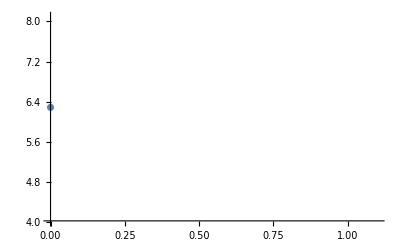

```mathematica
ListPlot[Table[{(j-1)/10,min[j]},{j, 1, 10}], PlotRange->{{0,1.1}, {4, 8.1}}]
```

Power::infy: Infinite expression 1/0. encountered.

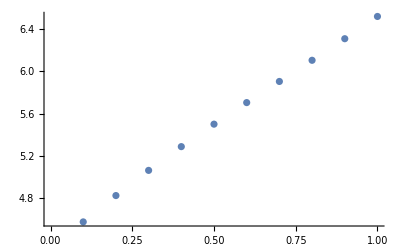

```mathematica
ListPlot[Table[{j,-2S2[0.5,j]},{j, 0, 1,0.1}]]
```

```mathematica
Hold[3+3]
```

Hold[3+3]